```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=Flatten[Import["./k1.dat"]]/197.33;
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
lam1dl=lam1[[1;;Length[k]]]*k^-2;
lam2dl=lam2[[1;;Length[k]]]*k^-1*131.0855454573;
```

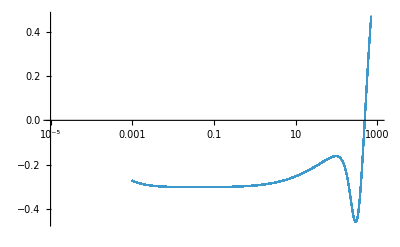

```mathematica
Show[ListPlot[Transpose[{k*197.33,lam1dl}],PlotRange->{{10^-5,1000},All},ScalingFunctions->{"Log",Automatic}]]
```

```mathematica
lam1dl[[-1]]
```

-0.272975

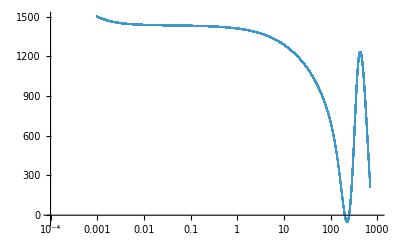

```mathematica
ListPlot[Transpose[{k*197.33,lam2dl}],PlotRange->{{10^-4,1000},All},ScalingFunctions->{"Log",Automatic}]
```

```mathematica
Log[10^-4/131.0855353573]
```

-14.0862